```mathematica
f1[x_] = (2 (1+ x^{-1}) Log[1+x] - 2);
f2[x_] = -2 x^{-1} (Sqrt[1-x^2] ArcCos[x] -Pi/2)-2;
```

```mathematica
Limit[(f2[x])^{-1}  x, x->0]
```

{2/π}

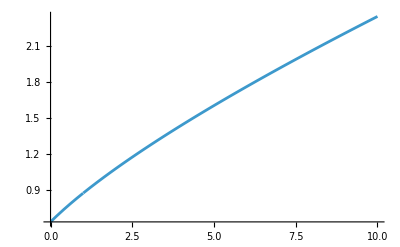

```mathematica
Plot[{f2[x]^{-1} x}, {x, 0,10}]
```

```mathematica
Manipulate[Plot[ {(f2[x])^{-1}  x, 2/π+b * x},{x,0,10}],{{b,0.18},0,4},{{c,0},-0.01, 0}]
```

```mathematica
Manipulate[Plot[ {1./(2/π +b*x), (f2[x])x^{-1}},{x,0,10}, PlotPoints->10000],{{b,0.18},0,4},{{c,0},-0.01, 0}]
```

```mathematica
Manipulate[Plot[ {(1+c  x)/(2/π +b*x)  f2[x]^{-1} x, 1.015, 0.985},{x,0,10}, PlotPoints->1000],{{b, 0.267},0,0.4},{{c,0.043},0., 0.1}]
```

```mathematica
b = 0.267; 
c = 0.043;
```